# Plotting the thermal power spectrum of a rectangular cantilever

```mathematica
x0={100*10^3,50*10^3,-.5*10^3}
v0={3,4,0}
a={0.08,0.06,0}
f={0.8,0.6,0}
```

{100000,50000,-500.}

{3,4,0}

{0.08,0.06,0}

{0.8,0.6,0}

```mathematica
x=x0+v0*100+1/2*a*10000
```

{100700.,50700.,-500.}

```mathematica
dx=x-x0
```

{700.,700.,0.}

```mathematica
f.dx
```

980.

```mathematica
? DotProduct
```

Information::notfound: Symbol "DotProduct" not found.

```mathematica
10.*Sqrt[v0.v0]
```

50.

```mathematica
1/Sqrt[1-0.5^2]
```

1.1547

```mathematica
(0.8-0.5)/(1-0.8*0.5)
```

0.5

```mathematica
NSolve[770^2==p^2+(2*140)^2,p]
```

{{p→-717.287},{p→717.287}}

```mathematica
717/2.
```

358.5

```mathematica
770/2.-140
```

245.

```mathematica
770/2/140.
```

2.75

```mathematica
f
```

{0.8,0.6,0}

```mathematica
Clear[f]
n=Sqrt[2*kB*T/(Pi*f0*k*Q)*1/((1-(f/f0)^2)^2+(f/(f0*Q))^2)]
```

√(2/π) √((kB T)/(f0 k ((1-f^2/f0^2)^2+f^2/(f0^2 Q^2)) Q))

```mathematica
Q=50;
k=0.02;
f0=18000;
kB=1.38*10^-23;
T=300;
```

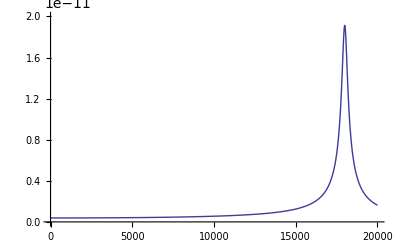

```mathematica
Plot[n,{f,0,20000},PlotRange->{0,0.2 10^-10}]
```